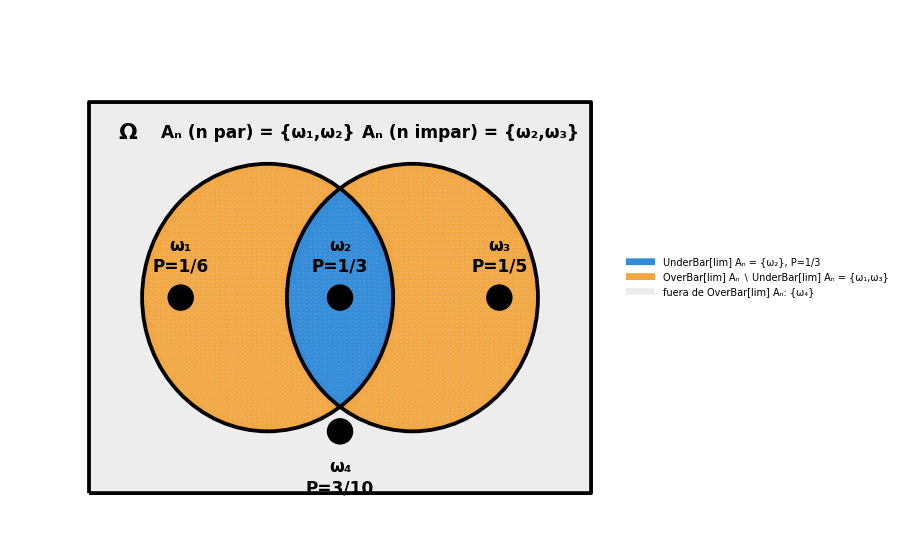

```mathematica
r = 1.3; sep = 0.75;
limX = 2.6; limY = 1.9;

pOmega = {1/6, 1/3, 1/5, 3/10}; (* P(ω1),...,P(ω4) *)

colorFuera = RGBColor[0.93, 0.93, 0.93];      (* fuera de limsup: ω4 *)
colorSoloLimsup = RGBColor[0.95, 0.65, 0.25]; (* en limsup \ liminf: ω1, ω3 *)
colorLiminf = RGBColor[0.2, 0.55, 0.85];      (* liminf = intersección: ω2 *)

pLiminf = pOmega[[2]];
pLimsup = pOmega[[1]] + pOmega[[2]] + pOmega[[3]];

grafico = Show[
   Graphics[{colorFuera, Rectangle[{-limX, -limY}, {limX, limY}]}],
   RegionPlot[
     ((x + sep)^2 + y^2 < r^2 && !((x - sep)^2 + y^2 < r^2)) ||
      ((x - sep)^2 + y^2 < r^2 && !((x + sep)^2 + y^2 < r^2)),
     {x, -limX, limX}, {y, -limY, limY},
     PlotStyle -> Directive[colorSoloLimsup, Opacity[0.85]],
     BoundaryStyle -> None, PlotPoints -> 100, MaxRecursion -> 3],
   RegionPlot[
     (x + sep)^2 + y^2 < r^2 && (x - sep)^2 + y^2 < r^2,
     {x, -limX, limX}, {y, -limY, limY},
     PlotStyle -> Directive[colorLiminf, Opacity[0.9]],
     BoundaryStyle -> None, PlotPoints -> 100, MaxRecursion -> 3],
   Graphics[{
     FaceForm[None], EdgeForm[{Black, Thickness[0.004]}],
     Rectangle[{-limX, -limY}, {limX, limY}],
     Black, Thickness[0.004], Circle[{-sep, 0}, r], Circle[{sep, 0}, r],

     Text[Style["Aₙ (n par) = {ω₁,ω₂}", 17, Bold], {-sep - 0.1, r + 0.3}],
     Text[Style["Aₙ (n impar) = {ω₂,ω₃}", 17, Bold], {sep + 0.6, r + 0.3}],
     Text[Style["Ω", 22, Bold], {-limX + 0.4, limY - 0.3}],

     PointSize[0.028], Black,
     Point[{-sep - 0.9, 0}], Point[{0, 0}], Point[{sep + 0.9, 0}], Point[{0, -1.3}],

     Text[Style["ω₁\nP=1/6", 17, Bold], {-sep - 0.9, 0.4}],
     Text[Style["ω₂\nP=1/3", 17, Bold], {0, 0.4}],
     Text[Style["ω₃\nP=1/5", 17, Bold], {sep + 0.9, 0.4}],
     Text[Style["ω₄\nP=3/10", 17, Bold], {0, -1.75}]
     }],
   PlotRange -> {{-limX - 0.1, limX + 0.1}, {-limY - 0.1, limY + 0.5}},
   AspectRatio -> Automatic, ImageSize -> 680
   ];

(* Etiquetas de leyenda con la notación correcta para conjuntos:
   liminf = UnderBar["lim"],  limsup = OverBar["lim"] *)
etiquetaLiminf = Row[{UnderBar[Style["lim", 17, Bold]],
    Style[" Aₙ = {ω₂},  P=1/3", 17, Bold]}];

etiquetaSoloLimsup = Row[{OverBar[Style["lim", 17, Bold]], Style[" Aₙ ∖ ", 17, Bold],
    UnderBar[Style["lim", 17, Bold]], Style[" Aₙ = {ω₁,ω₃}", 17, Bold]}];

etiquetaFuera = Row[{Style["fuera de ", 17, Bold], OverBar[Style["lim", 17, Bold]],
    Style[" Aₙ: {ω₄}", 17, Bold]}];

imagenFinal = Legended[grafico,
   SwatchLegend[{colorLiminf, colorSoloLimsup, colorFuera},
    {etiquetaLiminf, etiquetaSoloLimsup, etiquetaFuera},
    LabelStyle -> Directive[FontSize -> 17], LegendMarkerSize -> 22]];

imagenFinal
```

```mathematica
Export["prob_quesada_2_6_a.png",imagenFinal,Background->None,ImageResolution->600];
```